# Interactive visualisations for Cellular Automata (Rule 30).

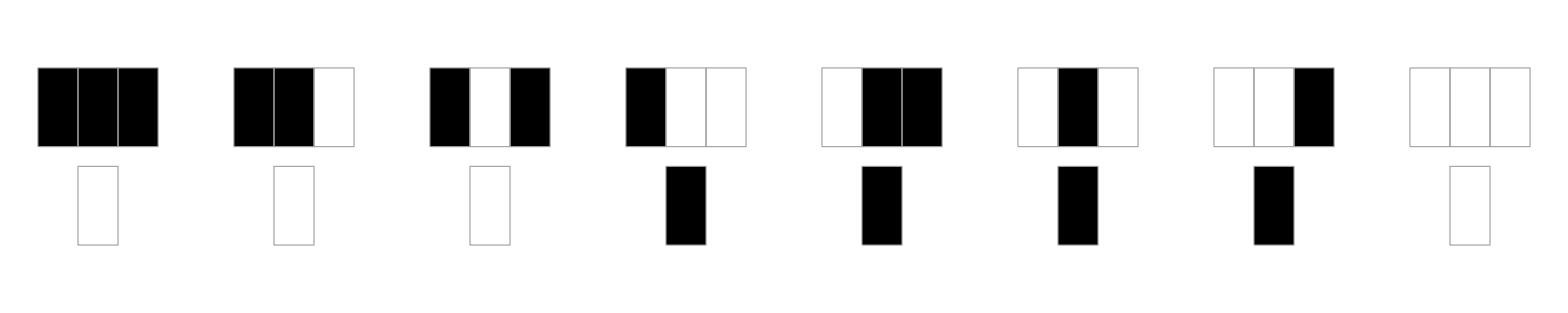

```mathematica
RulePlot[CellularAutomaton[30]]
```

## Visualisation 1

```mathematica
f1[a_]:=Join[l=CellularAutomaton[30,{{1},0},100][[1;;a+1]],Table[Table[0,Length[l[[1]]]],100-a-1]];
Manipulate[ArrayPlot[f1[x],Mesh->True,ImageSize->Full],{x,0,100,1}]
```

## Visualisation 2

```mathematica
f2[b_]:=CellularAutomaton[30,{{1},0},100][[1;;b+1]];
Manipulate[ArrayPlot[f2[i],Mesh->True,ImageSize->Full],{i,0,100,1}]
```